```mathematica
solsplantri8=FindFullFormula4[plantri8]
```

{v14acx29bdx357hx68efg,v14acx259dx37bhx68efg,v137gx24acx568fx9bdeh,v14acx259dfx37ghx68be,v14acx259dfx37bhx68eg,v14adx29bcx357hx68efg,v14adx259cx37bhx68efg,v137gx258acx4bdhx69ef,v137gx258acx46fx9bdeh,v1467x258acx3fgx9bdeh,v1467x258acx39bhxdefg,v146ax259dfx37ghx8bce,v146ax259dfx37bhx8ceg,v139cx25adx47bhx68efg,v13acx259dx47bhx68efg,v13acx247bx59dhx68efg,v139cx247bx5adhx68efg,v1467x28fgx35acx9bdeh,v13cgx259dfx467bx8aeh,v13acx259dfx467bx8egh,v13cgx259dfx47bhx68ae,v13acx259dfx47bhx68eg}

```mathematica
ToColors2[buckets_]:=Block[{index,  color,  result},
result={};
For[index=1,index≤Length[buckets],index++,
color= IndexToColor [index ];
Table[AppendTo[result,node->color],
{node,buckets[[index]]}];
];
result
]
```

```mathematica
ToColors2[SymbolToSets[v14acx29bdx357hx68efg]]
```

{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],11→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],15→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]}

```mathematica
Table[ToColors2[SymbolToSets[sol]],{sol,solsplantri8}]
```

{{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],11→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],15→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],15→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],3→RGBColor[1, 0, 0],7→RGBColor[1, 0, 0],16→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],4→RGBColor[0, 1, 0],10→RGBColor[0, 1, 0],12→RGBColor[0, 1, 0],5→RGBColor[0, 0, 1],6→RGBColor[0, 0, 1],8→RGBColor[0, 0, 1],15→RGBColor[0, 0, 1],9→RGBColor[1, 1, 0],11→RGBColor[1, 1, 0],13→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],17→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],15→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],16→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],11→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],15→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],13→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],11→RGBColor[0, 1, 0],12→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],15→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],13→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],12→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],15→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],3→RGBColor[1, 0, 0],7→RGBColor[1, 0, 0],16→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],8→RGBColor[0, 1, 0],10→RGBColor[0, 1, 0],12→RGBColor[0, 1, 0],4→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],13→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],9→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],15→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],3→RGBColor[1, 0, 0],7→RGBColor[1, 0, 0],16→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],8→RGBColor[0, 1, 0],10→RGBColor[0, 1, 0],12→RGBColor[0, 1, 0],4→RGBColor[0, 0, 1],6→RGBColor[0, 0, 1],15→RGBColor[0, 0, 1],9→RGBColor[1, 1, 0],11→RGBColor[1, 1, 0],13→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],17→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],6→RGBColor[1, 0, 0],7→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],8→RGBColor[0, 1, 0],10→RGBColor[0, 1, 0],12→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],15→RGBColor[0, 0, 1],16→RGBColor[0, 0, 1],9→RGBColor[1, 1, 0],11→RGBColor[1, 1, 0],13→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],17→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],6→RGBColor[1, 0, 0],7→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],8→RGBColor[0, 1, 0],10→RGBColor[0, 1, 0],12→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],9→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],13→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],15→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],6→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],15→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],16→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],8→RGBColor[1, 1, 0],11→RGBColor[1, 1, 0],12→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],6→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],15→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],8→RGBColor[1, 1, 0],12→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],3→RGBColor[1, 0, 0],9→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],10→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],4→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],15→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],3→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],4→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],15→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],3→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],4→RGBColor[0, 1, 0],7→RGBColor[0, 1, 0],11→RGBColor[0, 1, 0],5→RGBColor[0, 0, 1],9→RGBColor[0, 0, 1],13→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],15→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],3→RGBColor[1, 0, 0],9→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],4→RGBColor[0, 1, 0],7→RGBColor[0, 1, 0],11→RGBColor[0, 1, 0],5→RGBColor[0, 0, 1],10→RGBColor[0, 0, 1],13→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],15→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],6→RGBColor[1, 0, 0],7→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],8→RGBColor[0, 1, 0],15→RGBColor[0, 1, 0],16→RGBColor[0, 1, 0],3→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1],10→RGBColor[0, 0, 1],12→RGBColor[0, 0, 1],9→RGBColor[1, 1, 0],11→RGBColor[1, 1, 0],13→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],17→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],3→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],16→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],15→RGBColor[0, 1, 0],4→RGBColor[0, 0, 1],6→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],8→RGBColor[1, 1, 0],10→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],17→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],3→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],15→RGBColor[0, 1, 0],4→RGBColor[0, 0, 1],6→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],8→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0],17→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],3→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],16→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],15→RGBColor[0, 1, 0],4→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],10→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0]},{1→RGBColor[1, 0, 0],3→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],12→RGBColor[1, 0, 0],2→RGBColor[0, 1, 0],5→RGBColor[0, 1, 0],9→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0],15→RGBColor[0, 1, 0],4→RGBColor[0, 0, 1],7→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],17→RGBColor[0, 0, 1],6→RGBColor[1, 1, 0],8→RGBColor[1, 1, 0],14→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0]}}

```mathematica
Graph[EdgeList[plantri8],VertexStyle->{1->RGBColor[1, 0, 0],3->RGBColor[1, 0, 0],10->RGBColor[1, 0, 0],12->RGBColor[1, 0, 0],1->RGBColor[0, 1, 0],3->RGBColor[0, 1, 0],10->RGBColor[0, 1, 0],12->RGBColor[0, 1, 0],1->RGBColor[0, 0, 1],3->RGBColor[0, 0, 1],10->RGBColor[0, 0, 1],12->RGBColor[0, 0, 1],1->RGBColor[1, 1, 0],3->RGBColor[1, 1, 0],10->RGBColor[1, 1, 0],12->RGBColor[1, 1, 0]}, VertexLabels->Automatic, GraphLayout->"PlanarEmbedding"]
```

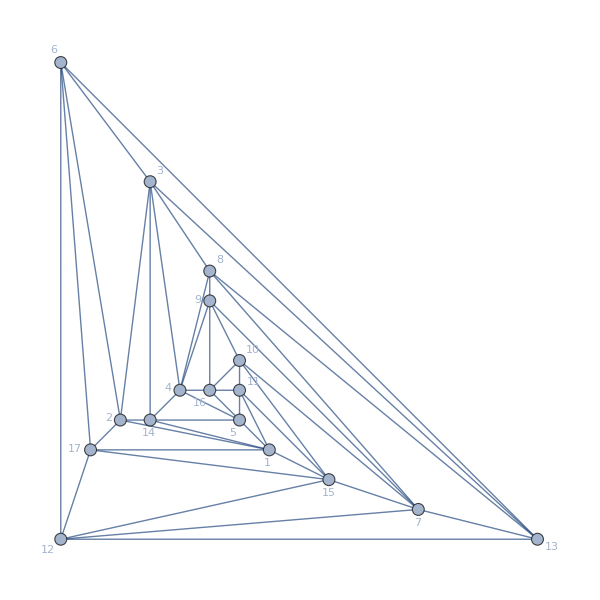
{-Graphics-v14acx29bdx357hx68efg,-Graphics-v14acx259dx37bhx68efg,-Graphics-v137gx24acx568fx9bdeh,-Graphics-v14acx259dfx37ghx68be,-Graphics-v14acx259dfx37bhx68eg,-Graphics-v14adx29bcx357hx68efg,-Graphics-v14adx259cx37bhx68efg,-Graphics-v137gx258acx4bdhx69ef,-Graphics-v137gx258acx46fx9bdeh,-Graphics-v1467x258acx3fgx9bdeh,-Graphics-v1467x258acx39bhxdefg,-Graphics-v146ax259dfx37ghx8bce,-Graphics-v146ax259dfx37bhx8ceg,-Graphics-v139cx25adx47bhx68efg,-Graphics-v13acx259dx47bhx68efg,-Graphics-v13acx247bx59dhx68efg,-Graphics-v139cx247bx5adhx68efg,-Graphics-v1467x28fgx35acx9bdeh,-Graphics-v13cgx259dfx467bx8aeh,-Graphics-v13acx259dfx467bx8egh,-Graphics-v13cgx259dfx47bhx68ae,-Graphics-v13acx259dfx47bhx68eg}

```mathematica
Table[Labeled[Graph[EdgeList[plantri8], VertexSize->Large,VertexStyle->ToColors2[SymbolToSets[sol]], VertexLabels->Automatic, GraphLayout->"PlanarEmbedding", ImageSize->600],sol],{sol,solsplantri8}]
```

```mathematica
SymbolToSets[v14acx29bdx357hx68efg]
```

{{1,4,10,12},{2,9,11,13},{3,5,7,17},{6,8,14,15,16}}

```mathematica
MissingGraph[mainGraph_,buckets_]:=Block[{result, highlight={},ed},
result=Subgraph[plantri8,Flatten[buckets],GraphHighlight->buckets[[1]], GraphLayout->"BipartiteEmbedding"];
Table[
ed=UndirectedEdge[edge[[1]],edge[[2]]];
If[!EdgeQ[result,ed],AppendTo[highlight, ed]],
{edge,Tuples[buckets]}
];
EdgeAdd[result, highlight, GraphHighlight->Join[buckets[[1]],highlight]]
]
```

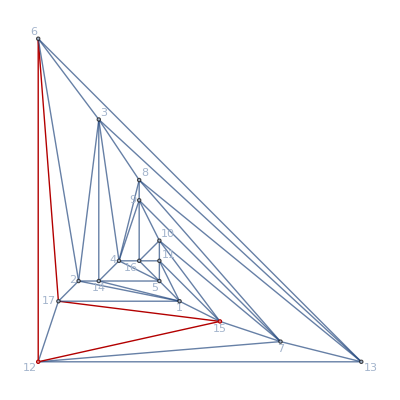

```mathematica
Graph[EdgeList[plantri8],GraphHighlight->{12,15,12<->15,15<->17,17<->6,6<->12}, GraphHighlightStyle->{"Thick"}, VertexLabels->Automatic, GraphLayout->"PlanarEmbedding"]
```

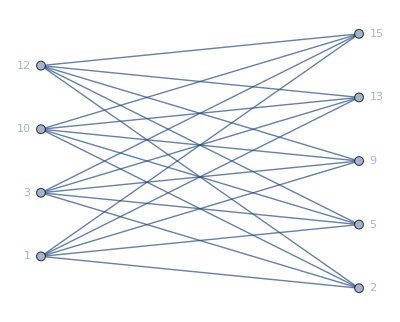
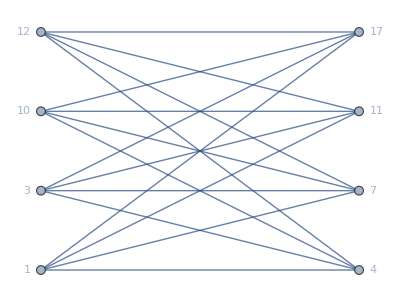
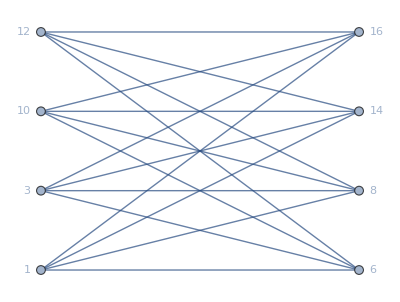
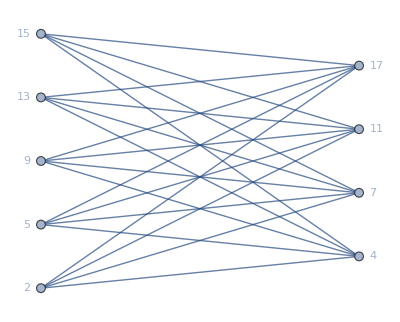
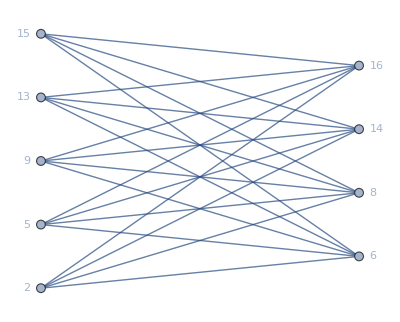
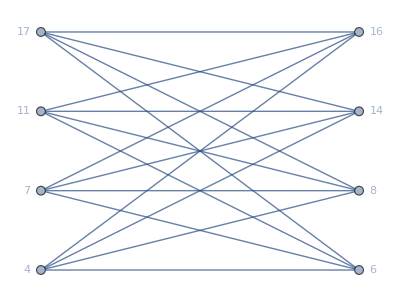
{-Graphics-13ac♁259df,-Graphics-13ac♁47bh,-Graphics-13ac♁68eg,-Graphics-259df♁47bh,-Graphics-259df♁68eg,-Graphics-47bh♁68eg}

```mathematica
Table[Labeled[MissingGraph[plantri8,bucket],SetsToLabel[bucket]],
{bucket,Subsets[SymbolToSets[v13acx259dfx47bhx68eg],{2}]}]
```

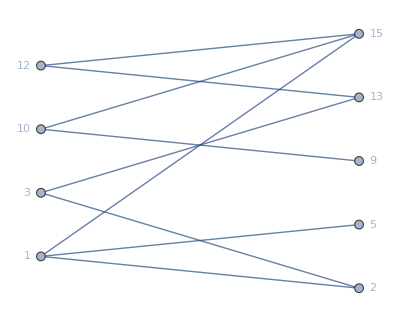
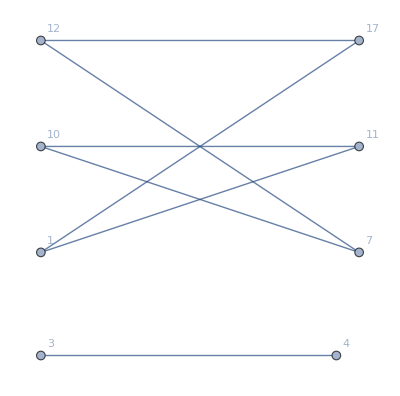
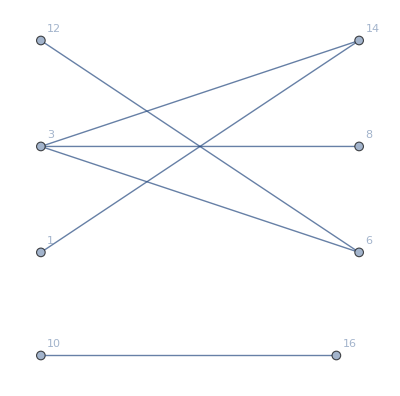
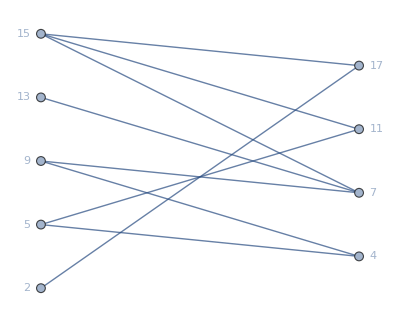
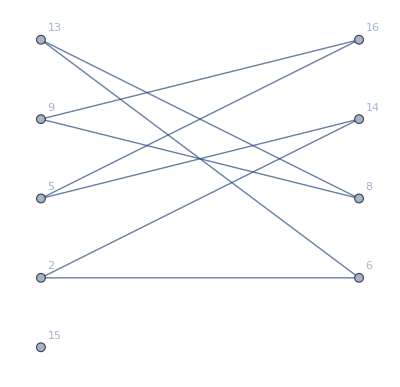
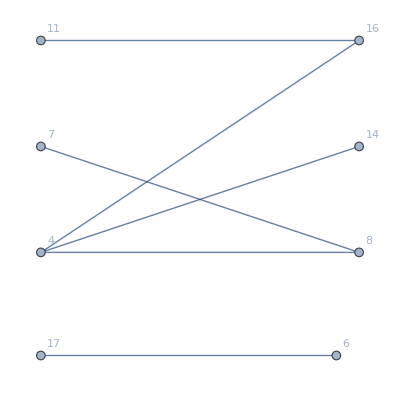
{-Graphics-13ac♁259df,-Graphics-13ac♁47bh,-Graphics-13ac♁68eg,-Graphics-259df♁47bh,-Graphics-259df♁68eg,-Graphics-47bh♁68eg}

```mathematica
Table[Labeled[
Subgraph[plantri8,Flatten[bucket],GraphHighlight->bucket[[1]], GraphLayout->"BipartiteEmbedding"],
SetsToLabel[bucket]],{bucket,Subsets[SymbolToSets[v13acx259dfx47bhx68eg],{2}]}]
```